# Ejercicio I.2: Representación gráfica de una red

## Nombre del Alumno: Felix Sanz Gonzalez DNI: 78997168b

```mathematica
Clear["Global`*"]
```

# 1.- Construir grafo de una cola SIMPLE

```mathematica
SetAttributes[createPrimitive,HoldAll]

createPrimitive[patt_,expr_]:=Typeset`MakeBoxes[p:patt,fmt_,Graphics]:=Typeset`MakeBoxes[Interpretation[expr,p],fmt,Graphics]
```

```mathematica
a=createPrimitive[face[x_: 0.1],
{Circle[{1.5 x,0},x],Line[{{-x,x},{0,x},{0,-x},{-x,-x}}],Line[{{0,0},{x/2,0}}]
}]
```

```mathematica
MakeBoxes[Interpretation[expr,p]]//DisplayForm
```

expr

```mathematica
InterpretationBox["expr",p]//DisplayForm
```

expr

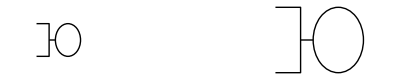

```mathematica
g=Show[Graphics[face[]],Graphics[Translate[face[0.2],{2,0}]]]
```

# 2.- Construir una topología gráfica de red

```mathematica
GraphPlot[{1->5,1->2,2->3,2->4,5->2,5->4,4->3},DirectedEdges->True,VertexLabeling->True,]
```

GraphPlot::argx: GraphPlot called with 4 arguments; 1 argument is expected.

GraphPlot[{1→5,1→2,2→3,2→4,5→2,5→4,4→3},DirectedEdges→True,VertexLabeling→True,Null]

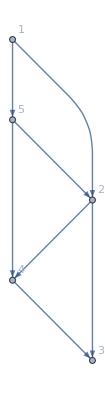

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
arrow=Graphics[face[0.01]];
```

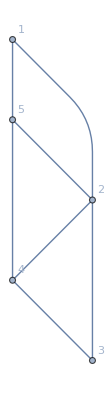
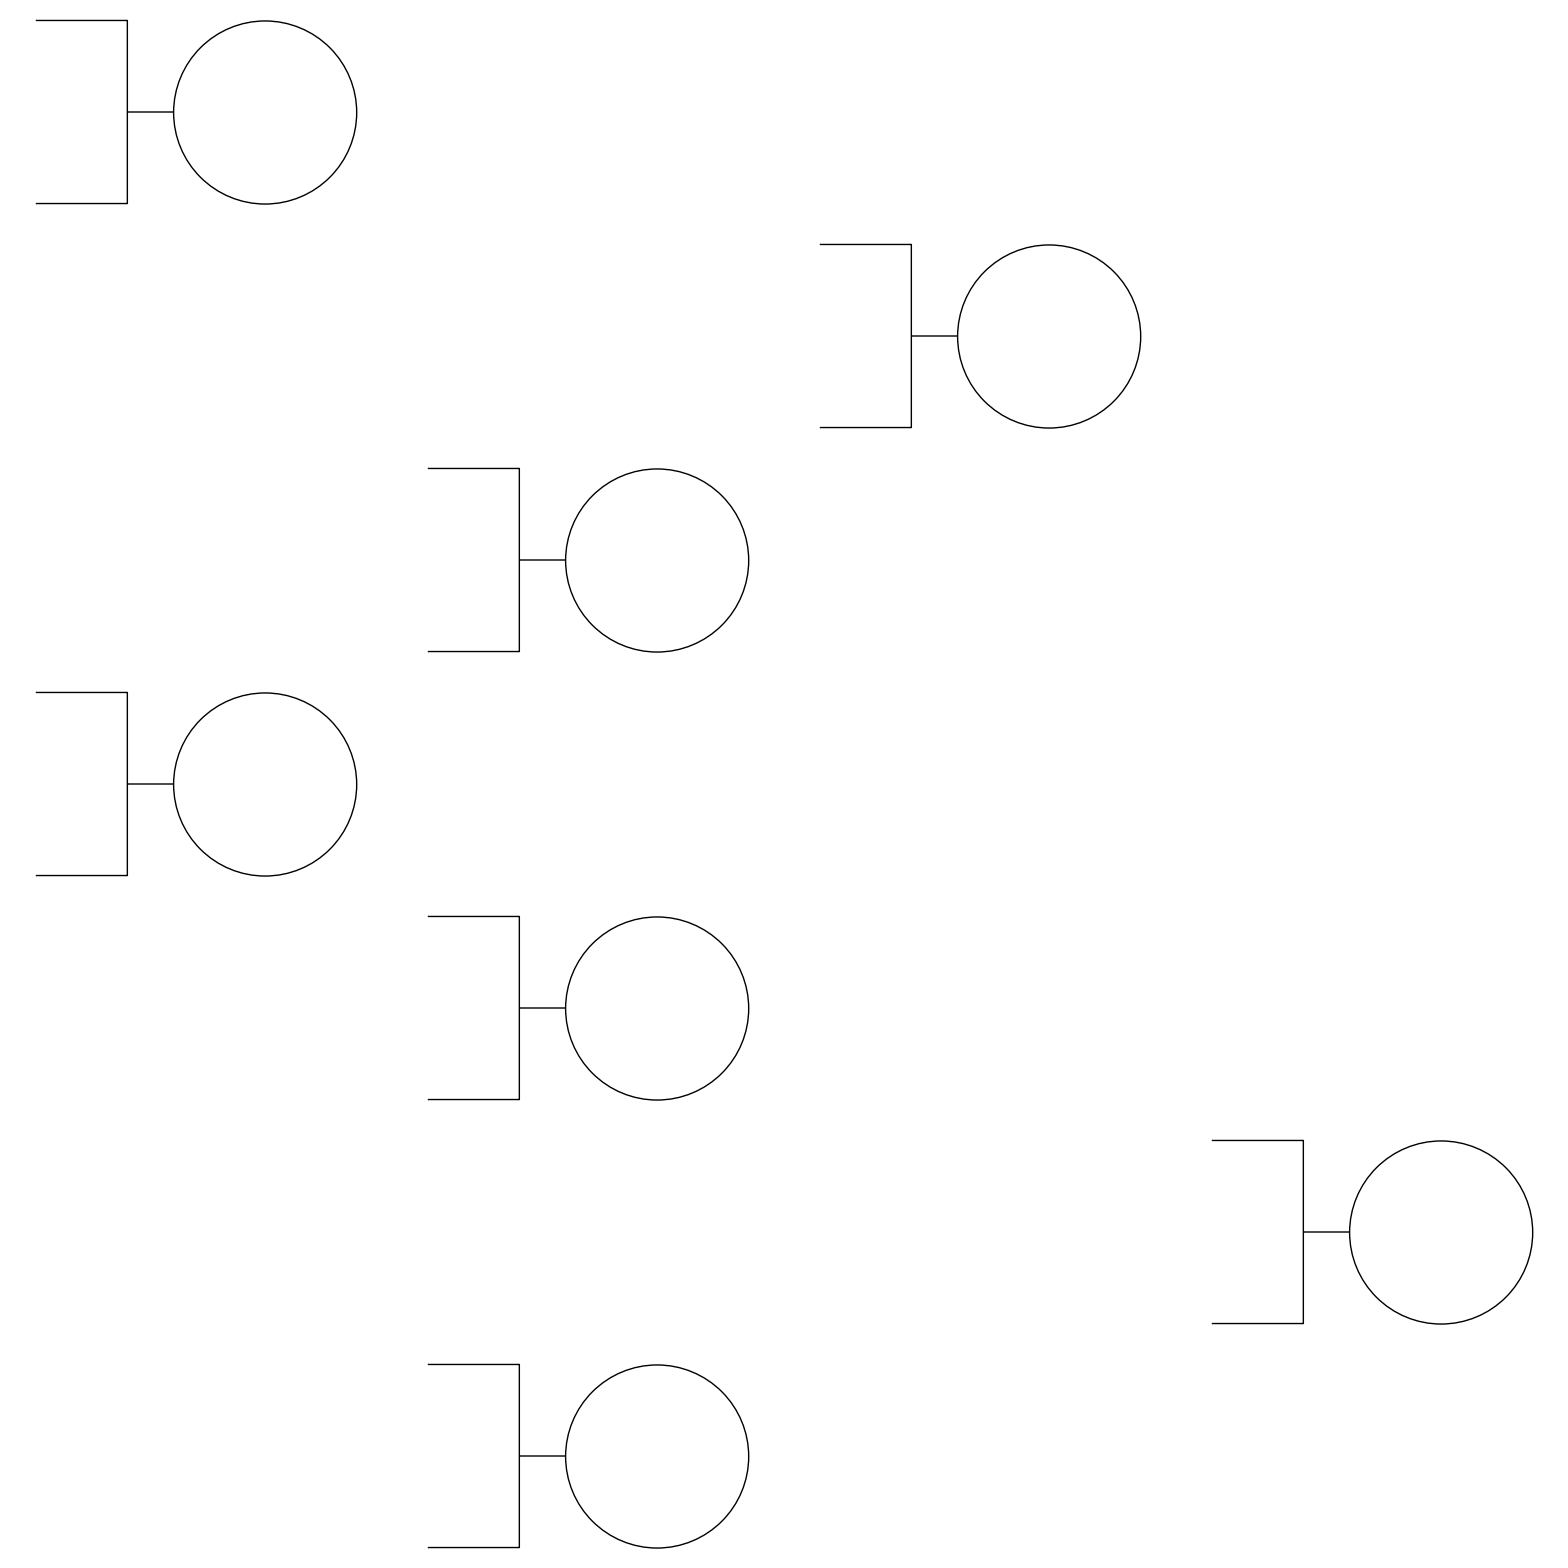

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4},DirectedEdges->True,VertexLabeling->True,EdgeRenderingFunction->({Line[#],Inset[arrow,Mean[#1],Automatic,0.3,#[[2]]-#[[1]],Background->White]}&)]
```

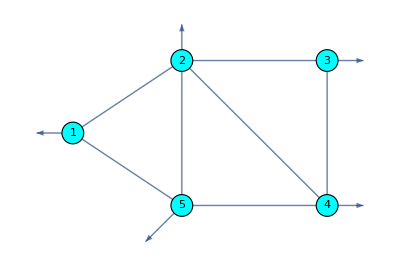
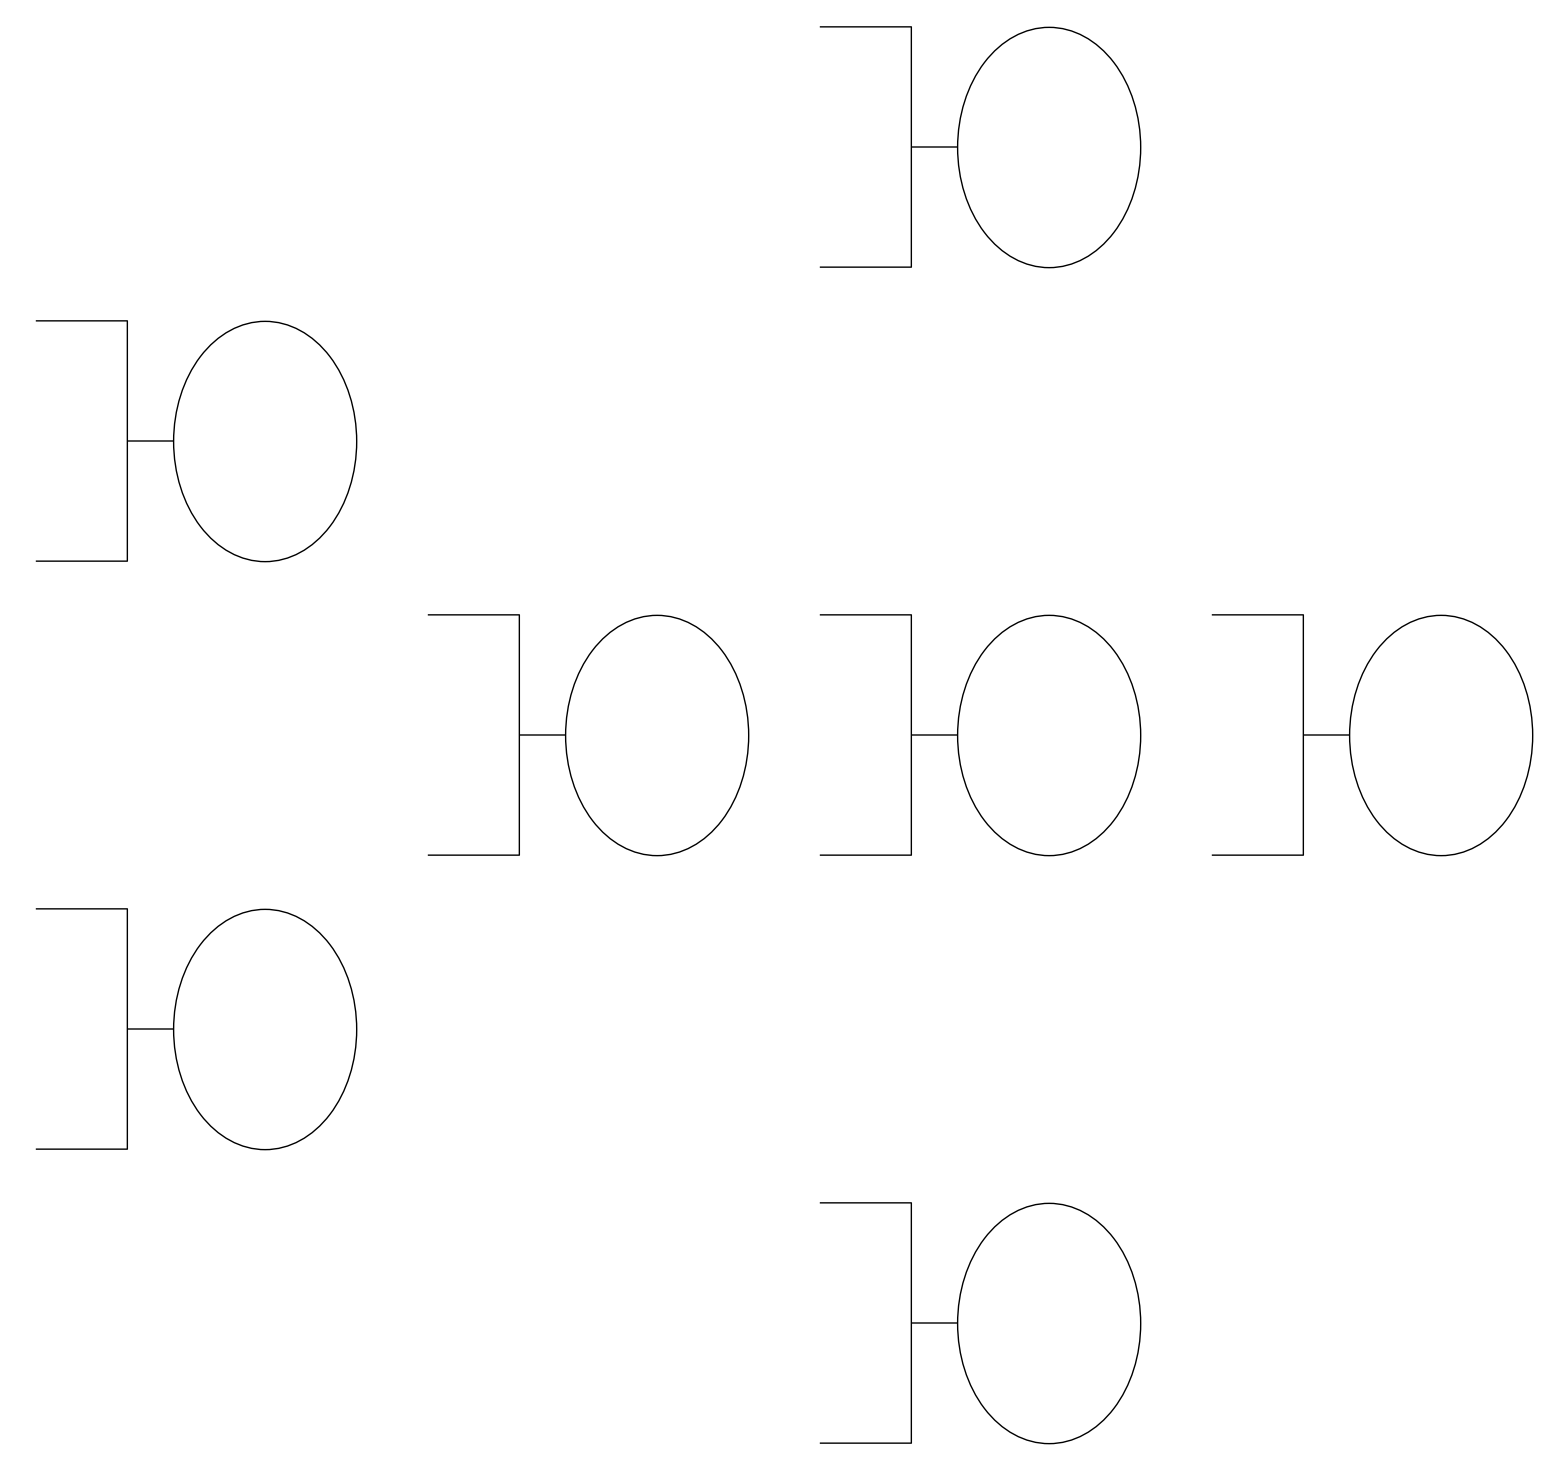

```mathematica
GraphPlot[{1->5,1->2,5->4,4->3,5->2,2->3,2->4,10->1,6->5,7->2,4->8,3->9},VertexCoordinateRules->{1->{0.5,0},2->{2,1},3->{4,1},4->{4,-1},5->{2,-1},6->{1.5,-1.5},7->{2,1.5},8->{4.5,-1},9->{4.5,1},10->{0,0}},VertexRenderingFunction->(If[#2≤5,{EdgeForm[Black],Cyan,Disk[#1,0.15],Black,Text[#2,#1]}]&),EdgeRenderingFunction-> (If[#2[[1]]≤5&&#2[[2]]≤5,{{Arrowheads[{0,.03,0,.03,.03}],Arrow[#1]},Inset[arrow,Mean[#1],Automatic,0.5,#[[2]]-#[[1]],Background->White]},{Arrowheads[{0,.03,.03}],Arrow[#1]}]&)
]
```

# 3.- Adaptar la topología de red física a una red de colas equivalente

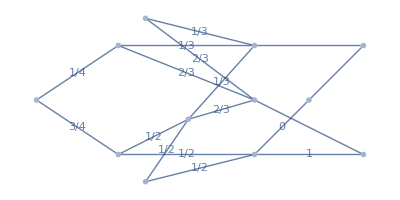

```mathematica
GraphPlot[{{{1,5}->{5,2},"1/2"},{{1,5}->{5,4},"1/2"},{{1,2}->{2,3},"1/3"},{{1,2}->{2,4},"2/3"},{{5,2}->{2,3},"1/3"},{{5,2}->{2,4},"2/3"},{{2,2}->{2,3},"1/3"},{{2,2}->{2,4},"2/3"},{{1,1}->{1,2},"1/4"},{{1,1}->{1,5},"3/4"},{{5,5}->{5,2},"1/2"},{{5,5}->{5,4},"1/2"},{2,4}->{4,4},{{5,4}->{4,4},"1"},{2,3}->{3,3},{{5,4}->{4,3},"0"},{4,3}->{3,3}},

VertexCoordinateRules->{{1,1}->{0,0},{1,2}->{1.5,1},{1,5}->{1.5,-1},{2,4}->{4,0},{5,5}->{2,-1.5},{2,3}->{4,1},{5,4}->{4,-1},{3,3}->{6,1},{4,4}->{6,-1},{2,2}->{2,1.5},{4,3}->{5,0}},VertexRenderingFunction-> ({Inset[arrow,#,Automatic,If[#2[[1]]==#2[[2]],0.2,0.5],If[#2=={5,2},{1,0.8},If[#2=={2,4},{2,-1},If[#2=={4,3},{1,1},{1,0}]]],Background->White]}&)
]
```

# 4.- Implementación del ejercicio con Queueing networks y sin protocolo

```mathematica
λ=2000; μ={3000,3000,3000,3000,3000,3000,3000,99999,99999};
```

```mathematica
γ={ (*Indicamos el caudal debido a los traficos externos que entran de forma directa*)
λ*1/4,(*Enlace A*)
λ*3/4,(*Enlace B*)
λ*1/2,(*Enlace C*)
λ*1/2,(*Enlace D*)
λ*1/3,(*Enlace E*)
λ*2/3,(*Enlace F*)
0,(*Enlace G*)
0,(*Enlace H*)
0   (*Enlace I*)
};

r={
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace A*)
{0,0,1/2,1/2,0,0,0,0,0}, (*Enlace B*)
{0,0,0,0,1/3,2/3,0,0,0}, (*Enlace C*)
{0,0,0,0,0,0,0,1,0}, (*Enlace D*)
{0,0,0,0,0,0,0,0,1}, (*Enlace E*)
{0,0,0,0,0,0,0,1,0},(*Enlace F*)
{0,0,0,0,0,0,0,0,1},(*Enlace G*)
{0,0,0,0,0,0,0,0,0},(*Enlace H*)
{0,0,0,0,0,0,0,0,0}    (*Enlace I*)
};

c={1,1,1,1,1,1,1,1,1};
𝒩=QueueingNetworkProcess[γ,r,μ,c];
```

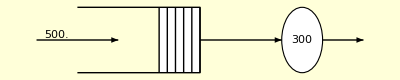
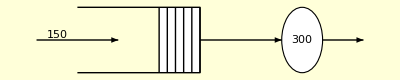
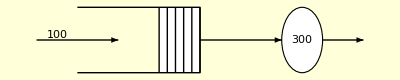
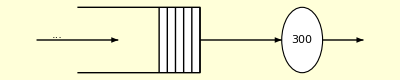
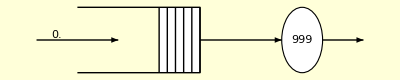
{-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 1.
Performance Measures | 
MeanSystemSize | 0.2
MeanSystemTime | 0.0004
MeanQueueSize | 0.0333333
MeanQueueTime | 0.0000666667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 2.
Performance Measures | 
MeanSystemSize | 1.
MeanSystemTime | 0.000666667
MeanQueueSize | 0.5
MeanQueueTime | 0.000333333,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 3.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.0008
MeanQueueSize | 0.816667
MeanQueueTime | 0.000466667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 4.
Performance Measures | 
MeanSystemSize | 1.4
MeanSystemTime | 0.0008
MeanQueueSize | 0.816667
MeanQueueTime | 0.000466667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 5.
Performance Measures | 
MeanSystemSize | 0.894737
MeanSystemTime | 0.000631579
MeanQueueSize | 0.422515
MeanQueueTime | 0.000298246,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 6.
Performance Measures | 
MeanSystemSize | 17.
MeanSystemTime | 0.006
MeanQueueSize | 16.0556
MeanQueueTime | 0.00566667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 8.
Performance Measures | 
MeanSystemSize | 0.0480354
MeanSystemTime | 0.0000104805
MeanQueueSize | 0.00220165
MeanQueueTime | 4.80359×10^-7,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 9.
SelectedNode | 9.
Performance Measures | 
MeanSystemSize | 0.0143704
MeanSystemTime | 0.0000101438
MeanQueueSize | 0.000203583
MeanQueueTime | 1.43705×10^-7}

```mathematica
{QueueProperties[{𝒩,1}]//N,QueueProperties[{𝒩,2}]//N,QueueProperties[{𝒩,3}]//N,QueueProperties[{𝒩,4}]//N,QueueProperties[{𝒩,5}]//N,QueueProperties[{𝒩,6}]//N,QueueProperties[{𝒩,8}]//N,QueueProperties[{𝒩,9}]//N}
```

```mathematica
data=RandomFunction[𝒩,{0,1}]["Path"];
data[[10;;15]]
```

{{0.000467405,{0,1,0,1,0,1,0,0,0}},{0.000514012,{0,1,0,2,0,1,0,0,0}},{0.000578144,{0,1,0,1,0,1,0,1,0}},{0.000585109,{0,1,0,1,0,1,0,0,0}},{0.000603207,{0,0,1,1,0,1,0,0,0}},{0.000623071,{0,0,1,0,0,1,0,1,0}}}

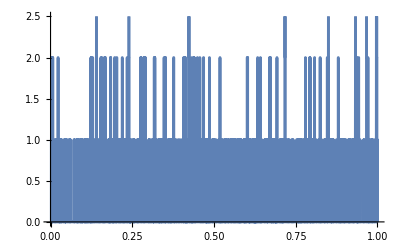
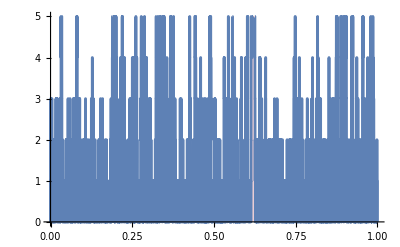
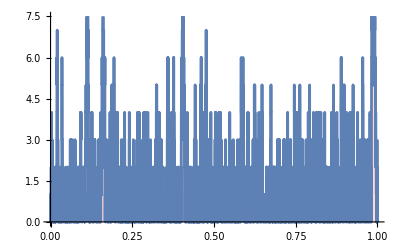
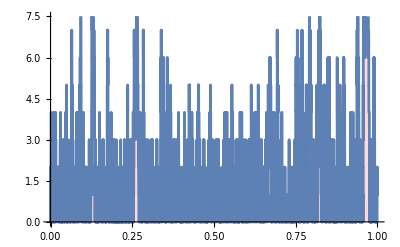
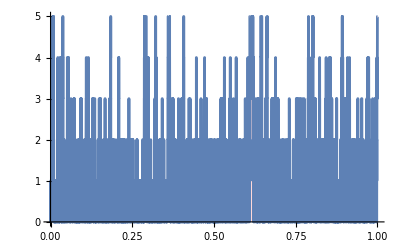
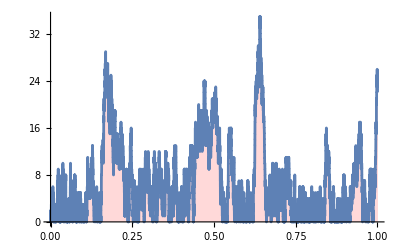
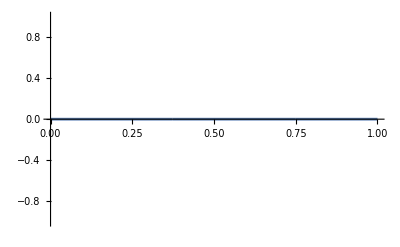
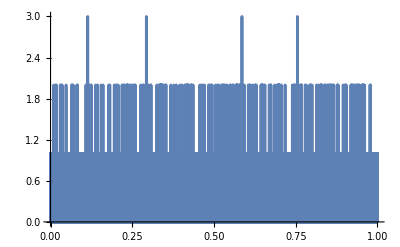

```mathematica
Table[ListLinePlot[Table[{data[[i,1]],data[[i,2,j]]},{i,Length[data]}],Filling->Axis,FillingStyle->LightRed],{j,9}]
```

# 4.- Implementación del ejercicio con Queueing networks con protocolos S&W y GBN: